```mathematica
Partition[Characters["Wolfram Language"],12,1]//Grid[#,Frame->All]&
```

W | o | l | f | r | a | m |   | L | a | n | g
o | l | f | r | a | m |   | L | a | n | g | u
l | f | r | a | m |   | L | a | n | g | u | a
f | r | a | m |   | L | a | n | g | u | a | g
r | a | m |   | L | a | n | g | u | a | g | e

```mathematica
NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},2]
```

{{{1}},{{1,0},{1,1}},{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,1,1,1}}}

```mathematica
{{#,0},{#,#}}&@{{1,0},{1,1}}
```

{{{{1,0},{1,1}},0},{{{1,0},{1,1}},{{1,0},{1,1}}}}

```mathematica
ArrayFlatten[{{{{1,0},{1,1}},0},{{{1,0},{1,1}},{{1,0},{1,1}}}}]
```

{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,1,1,1}}

```mathematica
{{{{1,0},{1,1}},0},{{{1,0},{1,1}},{{1,0},{1,1}}}}//Grid
```

{{1,0},{1,1}} | 0
{{1,0},{1,1}} | {{1,0},{1,1}}

```mathematica
{{{{1,0},{1,1}},0},{{{1,0},{1,1}},{{1,0},{1,1}}}}//ArrayFlatten//Grid
```

1 | 0 | 0 | 0
1 | 1 | 0 | 0
1 | 0 | 1 | 0
1 | 1 | 1 | 1

```mathematica
Riffle[{0,1,2},{3,4,5}]
```

{0,3,1,4,2,5}

```mathematica
Partition[Grid[#]&/@ArrayFlatten[{{{{1,0},{1,1}},{{0,0},{0,0}}},{{{1,0},{1,1}},{{1,0},{1,1}}}},1],2]//Grid[#,Frame->All]&
```

1 | 0
1 | 1 | 0 | 0
0 | 0
1 | 0
1 | 1 | 1 | 0
1 | 1

```mathematica
Grid[Partition[IntegerDigits[2^1000],50],Frame->All]
```

1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3

```mathematica
Range[0,5]
```

{0,1,2,3,4,5}

```mathematica
Last[GatherBy[Flatten[Table[{x,y,Sqrt[x^2+y^2]},{x,20},{y,20}],1],IntegerQ[Last[#]]&]]
```

{{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}}

```mathematica
IntegerQ[Last[#]]&[{20,15,25}]
```

True

```mathematica
Last[#]&[{20,15,25}]
```

25

```mathematica
Table[Max[Length/@Split[IntegerDigits[2^n]]],{n,100}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
GatherBy[Table[IntegerName[n],{n,100}],First[Characters[#]]&]
```

{{one,one hundred},{two,three,ten,twelve,thirteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine},{four,five,fourteen,fifteen,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine},{six,seven,sixteen,seventeen,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine},{eight,eleven,eighteen,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine},{nine,nineteen,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine}}

```mathematica
Tuples[{1,2},3]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

```mathematica
GatherBy[RandomChoice[WordList[],20],StringLength[#]&]
```

{{aspartame,obscenely,waveguide,adumbrate,glorified,disabling},{via},{clipping},{groyne,citrus,homing,triple},{prodigally,burdensome,hyperbolic},{chignon,passion,glacial,launder},{plump}}

```mathematica
Complement[Alphabet["Ukrainian"],Alphabet["Russian"]]
```

{є,і,ї,ґ}

```mathematica
Complement[{1,2,3},{2,3,4}]
```

{1}

```mathematica
Intersection[Range[100]^2,Range[100]^3]
```

{1,64,729,4096}

```mathematica
Intersection[EntityList[EntityClass["Country","NATO"]],EntityList[EntityClass["Country","GroupOf8"]]]
```

{Canada,France,Germany,Italy,United Kingdom,United States}

```mathematica
Tuples[{1,2},3]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

```mathematica
Table[StringJoin[RandomChoice[Alphabet[],5]],10]
```

{mqpzx,anqyt,ulfru,fnmqe,btxeq,cbxyw,mqdbr,ucxgr,cbxgs,xeeyp}

```mathematica
SortBy[IntegerName[Range[20]],StringLength]
```

{one,six,ten,two,five,four,nine,eight,seven,three,eleven,twelve,twenty,fifteen,sixteen,eighteen,fourteen,nineteen,thirteen,seventeen}

```mathematica
IntegerName[Range[20]]
```

{one,two,three,four,five,six,seven,eight,nine,ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen,twenty}

```mathematica
Transpose[Permutations[{1,2,3,4}]]//Grid
```

1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1

```mathematica
Intersection[Table[StringJoin[RandomChoice[Alphabet[],4]],1000],WordList[]]
```

{ajar,axle,lube,shoe}

```mathematica
Blend/@Tuples[{Red,Green,Blue},2]
```

{RGBColor[1, 0, 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[0, 1, 0],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[0, 0, 1]}

```mathematica
Union[{a,a,a,b,b}]
```

{a,b}

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2;;,1]]
```

{d,g}

```mathematica
Take[IntegerDigits[2^1000],-5]
```

{6,9,3,7,6}

```mathematica
Partition[Alphabet[],2][[All,2]]
```

{b,d,f,h,j,l,n,p,r,t,v,x,z}

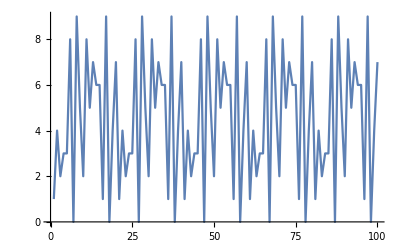

4096

```mathematica
Flatten[Part[IntegerDigits[12^#],-2]&/@Range[100]]//ListLinePlot
```

```mathematica
Cases[IntegerDigits[Range[1000]],{x_,x_,x_}]
```

{{1,1,1},{2,2,2},{3,3,3},{4,4,4},{5,5,5},{6,6,6},{7,7,7},{8,8,8},{9,9,9}}

```mathematica
Cases[IntegerDigits[Range[1000]^2],{9,__,1}|{9,__,0}]
```

{{9,0,0},{9,6,1},{9,8,0,1},{9,0,0,0,0},{9,0,6,0,1},{9,5,4,8,1},{9,6,1,0,0},{9,6,7,2,1},{9,0,0,6,0,1},{9,0,2,5,0,0},{9,0,4,4,0,1},{9,1,9,6,8,1},{9,2,1,6,0,0},{9,2,3,5,2,1},{9,3,8,9,6,1},{9,4,0,9,0,0},{9,4,2,8,4,1},{9,5,8,4,4,1},{9,6,0,4,0,0},{9,6,2,3,6,1},{9,7,8,1,2,1},{9,8,0,1,0,0},{9,8,2,0,8,1},{9,9,8,0,0,1}}

```mathematica
IntegerDigits[Range[100]]/.{0->Gray,9->Orange}
```

{{1},{2},{3},{4},{5},{6},{7},{8},{RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5]},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,RGBColor[1, 0.5, 0]},{2,GrayLevel[0.5]},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,RGBColor[1, 0.5, 0]},{3,GrayLevel[0.5]},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,RGBColor[1, 0.5, 0]},{4,GrayLevel[0.5]},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,RGBColor[1, 0.5, 0]},{5,GrayLevel[0.5]},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,RGBColor[1, 0.5, 0]},{6,GrayLevel[0.5]},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,RGBColor[1, 0.5, 0]},{7,GrayLevel[0.5]},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,RGBColor[1, 0.5, 0]},{8,GrayLevel[0.5]},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,RGBColor[1, 0.5, 0]},{RGBColor[1, 0.5, 0],GrayLevel[0.5]},{RGBColor[1, 0.5, 0],1},{RGBColor[1, 0.5, 0],2},{RGBColor[1, 0.5, 0],3},{RGBColor[1, 0.5, 0],4},{RGBColor[1, 0.5, 0],5},{RGBColor[1, 0.5, 0],6},{RGBColor[1, 0.5, 0],7},{RGBColor[1, 0.5, 0],8},{RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5],GrayLevel[0.5]}}

```mathematica
Characters["The Wolfram Language"]/.{"a"|"e"|"i"|"o"|"u"->Nothing}
```

{T,h, ,W,l,f,r,m, ,L,n,g,g}

```mathematica
IntegerDigits[2^1000]/.{0->Red}
```

{1,RGBColor[1, 0, 0],7,1,5,RGBColor[1, 0, 0],8,6,RGBColor[1, 0, 0],7,1,8,6,2,6,7,3,2,RGBColor[1, 0, 0],9,4,8,4,2,5,RGBColor[1, 0, 0],4,9,RGBColor[1, 0, 0],6,RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],1,8,1,RGBColor[1, 0, 0],5,6,1,4,RGBColor[1, 0, 0],4,8,1,1,7,RGBColor[1, 0, 0],5,5,3,3,6,RGBColor[1, 0, 0],7,4,4,3,7,5,RGBColor[1, 0, 0],3,8,8,3,7,RGBColor[1, 0, 0],3,5,1,RGBColor[1, 0, 0],5,1,1,2,4,9,3,6,1,2,2,4,9,3,1,9,8,3,7,8,8,1,5,6,9,5,8,5,8,1,2,7,5,9,4,6,7,2,9,1,7,5,5,3,1,4,6,8,2,5,1,8,7,1,4,5,2,8,5,6,9,2,3,1,4,RGBColor[1, 0, 0],4,3,5,9,8,4,5,7,7,5,7,4,6,9,8,5,7,4,8,RGBColor[1, 0, 0],3,9,3,4,5,6,7,7,7,4,8,2,4,2,3,RGBColor[1, 0, 0],9,8,5,4,2,1,RGBColor[1, 0, 0],7,4,6,RGBColor[1, 0, 0],5,RGBColor[1, 0, 0],6,2,3,7,1,1,4,1,8,7,7,9,5,4,1,8,2,1,5,3,RGBColor[1, 0, 0],4,6,4,7,4,9,8,3,5,8,1,9,4,1,2,6,7,3,9,8,7,6,7,5,5,9,1,6,5,5,4,3,9,4,6,RGBColor[1, 0, 0],7,7,RGBColor[1, 0, 0],6,2,9,1,4,5,7,1,1,9,6,4,7,7,6,8,6,5,4,2,1,6,7,6,6,RGBColor[1, 0, 0],4,2,9,8,3,1,6,5,2,6,2,4,3,8,6,8,3,7,2,RGBColor[1, 0, 0],5,6,6,8,RGBColor[1, 0, 0],6,9,3,7,6}

```mathematica
Select[IntegerDigits[2^1000],#==0||#==1&]
```

{1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,0}

```mathematica
Thread[Drop[Range[0,9],2]->Nothing]
```

{2→Nothing,3→Nothing,4→Nothing,5→Nothing,6→Nothing,7→Nothing,8→Nothing,9→Nothing}

```mathematica
IntegerDigits[2^1000]/.Thread[Drop[Range[0,9],2]->Nothing]
```

{1,0,1,0,0,1,0,0,0,0,0,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,1,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,1,0,0}